## Input

### Spanning tree

```mathematica
ClearAll[SpanningTree]

(* simple Kruskal's algorithm without sorting *)
SpanningTree[graph_]:=Module[{label,edges=EdgeList[graph]},Pick[edges,Table[If[UnsameQ[#1,#2],#2=#1;True,False]&@@Sort[label/@edge],{edge,edges}]]]
```

### Find faces

```mathematica
ClearAll[makeEges,FindFace,$faces,iteration,Faces]

makeEges[list_]:=Sort/@UndirectedEdge@@@Partition[list,2,1]

(* FindFace : finds the smallest cycle. This cycle is a pseudo-face. *)
FindFace[graph_,edges_]:=MapAt[makeEges,First@SortBy[Transpose[{FindShortestPath[graph,Sequence@@#]&/@edges,edges}],Composition[Length,First]],1]

(* Append analyzed edge to a graph *)
appendEge[graph_,edge_]:=Graph@Append[EdgeList[graph],edge]

iteration[graph_,{}]:=$faces;
iteration[graph_,edges_]:=iteration[AppendTo[$faces,Flatten[#]];appendEge[graph,Last@#],DeleteCases[edges,Last@#]]&[FindFace[graph,edges]]

(* Faces : returns all pseudo-faces of a graph *)
Faces[graph_]:=Block[{$faces={},tree=SpanningTree[graph]},
iteration[Graph[tree],Complement[EdgeList[graph],tree]]]
```

### Make dual graph

```mathematica
shareQ[set1_,set2_]:=Length@Intersection[set1,set2]>0;

(* connecting all faces *)
innerDualEdges[faces_]:=Join@@Table[
Table[If[shareQ@@faces⟦{i,j}⟧,UndirectedEdge[i,j],Unevaluated@Sequence[]],
{j,i+1,Length[faces]}],{i,1,Length[faces]-1}]

(* next two functions find the faces on the boundary *)
boundaryEdges[faces_]:=Module[{edges=Join@@faces},Select[Union[edges],(Count[edges,#]==1)&]]
boundaryFaces[faces_,outerEdges_]:=Select[Range@Length@faces,shareQ[faces⟦#⟧,outerEdges]&];

(** alltogather *)
DualGraph[faces_]:=Graph[DeleteDuplicates@Join[Thread@UndirectedEdge[0,boundaryFaces[faces,boundaryEdges[faces]]],innerDualEdges[faces]]]
```

## Output

```mathematica
graph=GridGraph[{5,9}];
```

### Spanning tree

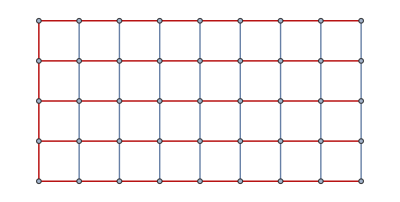

```mathematica
HighlightGraph[graph,SpanningTree[graph]]
```

### Faces

```mathematica
faces=Faces[graph];
```

```mathematica
images=Table[Rasterize@HighlightGraph[graph,faces⟦n⟧],{n,1,Length@faces}];
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["faces.gif",images]
```

faces.gif

```mathematica
Manipulate[HighlightGraph[graph,faces⟦n⟧],{n,1,Length@faces,1}]
```

### Dual graph

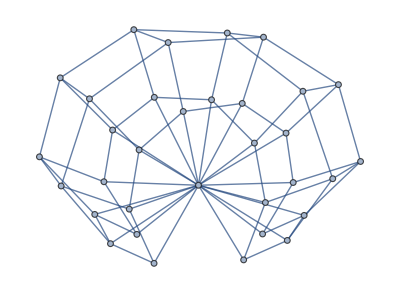

```mathematica
DualGraph[faces]
```

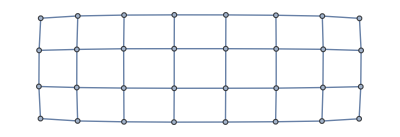

```mathematica
Graph[innerDualEdges[faces]]
```

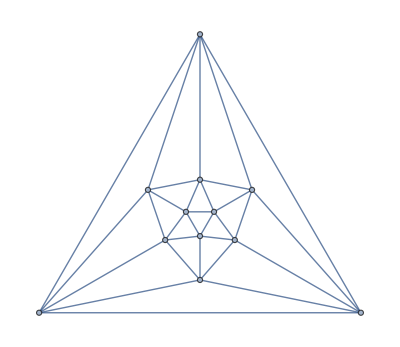
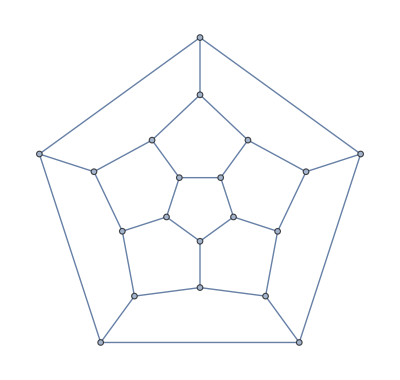
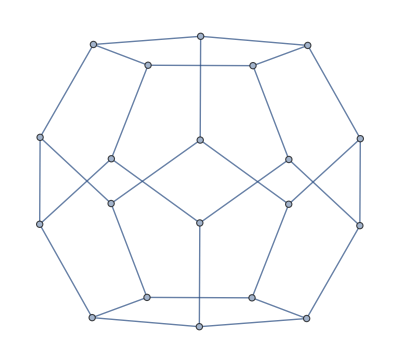

```mathematica
{GraphData["IcosahedralGraph"],GraphData["IcosahedralGraph","DualGraph"],DualGraph[Faces[GraphData["IcosahedralGraph"]]]}
```

```mathematica
IsomorphicGraphQ[GraphData["IcosahedralGraph","DualGraph"],DualGraph[Faces[GraphData["IcosahedralGraph"]]]]
```

True